# Decoherence

```mathematica
<<Q3`
<<Q3`Kraus`
```

```mathematica
Let[Qubit,S]
```

## Quantum Operations

## Generalized Measurement as Quantum Operations

## Quantum Master Equations

### Derivation

### Examples

### Solution Methods

Consider the Lindblad equation for a single-qubit system with the effective Hamiltonian and the Lindblad operators as following:

```mathematica
Let[Real,Ω,Δ,Γ]
```

```mathematica
opH=Δ S[1]/2+Ω S[3]/2
opL={Sqrt[Γ["+"]]S[4],Sqrt[Γ["-"]]S[5]}
```

(Δ S^x)/2+(Ω S^z)/2

{S^+ √(Γ_+),S^- √(Γ_-)}

This is the naive form of the generator matrix corresponding to the Lindblad equation without taking into account the Hemicity condition and the probability conservation condition.

```mathematica
mat=ChoiMatrix@LindbladGenerator[opH,opL];
mat=ArrayReshape[Transpose[mat,2<->3],{4,4}];
mat//MatrixForm
```

(-Γ_- | (ⅈ Δ)/2 | -(ⅈ Δ)/2 | Γ_+
(ⅈ Δ)/2 | -ⅈ Ω-(Γ_-)/2-(Γ_+)/2 | 0 | -(ⅈ Δ)/2
-(ⅈ Δ)/2 | 0 | ⅈ Ω-(Γ_-)/2-(Γ_+)/2 | (ⅈ Δ)/2
Γ_- | -(ⅈ Δ)/2 | (ⅈ Δ)/2 | -Γ_+)

```mathematica
ρ[1,1]=z;
ρ[1,2]=x+I y;
ρ[2,1]=x+I y;
ρ[2,2]=1-ρ[1,1];
```

```mathematica
expr=mat.rho
dv=Coefficient[#,{z,x,y}]&/@expr
```

{-z Γ_-+(1-z) Γ_+,-1/2 ⅈ (1-z) Δ+(ⅈ z Δ)/2+(x+ⅈ y) (-ⅈ Ω-(Γ_-)/2-(Γ_+)/2),1/2 ⅈ (1-z) Δ-(ⅈ z Δ)/2+(x+ⅈ y) (ⅈ Ω-(Γ_-)/2-(Γ_+)/2),z Γ_--(1-z) Γ_+}

{{-Γ_--Γ_+,0,0},{ⅈ Δ,-ⅈ Ω-(Γ_-)/2-(Γ_+)/2,Ω-(ⅈ Γ_-)/2-(ⅈ Γ_+)/2},{-ⅈ Δ,ⅈ Ω-(Γ_-)/2-(Γ_+)/2,-Ω-(ⅈ Γ_-)/2-(ⅈ Γ_+)/2},{Γ_-+Γ_+,0,0}}

```mathematica
matK={dv[[1]],
(dv[[2]]+dv[[3]])/2,
-(dv[[2]]-dv[[3]])/2}//Simplify;
matK//MatrixForm
```

(-Γ_--Γ_+ | 0 | 0
0 | 1/2 (-Γ_--Γ_+) | -1/2 ⅈ (Γ_-+Γ_+)
-ⅈ Δ | ⅈ Ω | -Ω)

```mathematica
off={expr[[1]],(expr[[2]]+expr[[3]])/2,I(expr[[2]]-expr[[3]])/2}/.{z->0,x->0,y->0}
```

{Γ_+,0,Δ/2}

Let us consider a single qubit, and examine a master equation. We assume that the system is initially prepared in a pure state (0+1)/√2.

```mathematica
init=(1+S[1])/2;
init//MatrixForm
```

1/2 (1+S^x)

This is the effective Hamiltonian.

```mathematica
opH=S[3];
```

These are the Lindblad operators.

```mathematica
Let[Real,Γ]
opL={Sqrt[Γ["+"]] S[4],Sqrt[Γ["-"]]S[5]}
```

{S^+ √(Γ_+),S^- √(Γ_-)}

This is the Lindblad basis we are going to use. It happens to be equivalent to the basis consisting of the Pauli operators.

```mathematica
lbs=LindbladBasis[S]
MatrixForm/@(Matrix[#,S]&)/@lbs
```

{1/(√2),S^z/(√2),S^x/(√2),S^y/(√2)}

{(1/(√2) | 0
0 | 1/(√2)),(1/(√2) | 0
0 | -1/(√2)),(0 | 1/(√2)
1/(√2) | 0),(0 | -ⅈ/(√2)
ⅈ/(√2) | 0)}

Here are the generator matrix K and the inhomogeneous term when the Lindblad equation is written in the standard form of an inhomogeneous first-order differential equation.

```mathematica
{mat,vec}=LindbladConvert[opH,opL];
mat//MatrixForm
vec//MatrixForm
```

(-Γ_--Γ_+ | 0 | 0
0 | 1/2 (-2 ⅈ-(Γ_-)/2-(Γ_+)/2)+1/2 (2 ⅈ-(Γ_-)/2-(Γ_+)/2) | -1/2 ⅈ (-2 ⅈ-(Γ_-)/2-(Γ_+)/2)+1/2 ⅈ (2 ⅈ-(Γ_-)/2-(Γ_+)/2)
0 | 1/2 ⅈ (-2 ⅈ-(Γ_-)/2-(Γ_+)/2)-1/2 ⅈ (2 ⅈ-(Γ_-)/2-(Γ_+)/2) | 1/2 (-2 ⅈ-(Γ_-)/2-(Γ_+)/2)+1/2 (2 ⅈ-(Γ_-)/2-(Γ_+)/2))

((-Γ_-+Γ_+)/(√2)
0
0)

This solves the differential equation based on the generator matrix K and the inhomogeneous term.

```mathematica
Clear[ρ]
ρ[t_]=Block[
{Γ,ρ},
Γ["+"]=.3;
Γ["-"]=.7;
LindbladSolve[opH,opL,init,t]//Chop
];
ρ[t]//MatrixForm
```

0.5+0.5 ⅇ^(-0.5 t) Cos[2. t] S^x+(-0.2+0.2 ⅇ^(-1. t)) S^z+0.5 ⅇ^(-0.5 t) S^y Sin[2. t]

To investigate the physical properties of the solution, we calculate the expectation values of the Pauli operators.

```mathematica
{avgX[t_],avgY[t_],avgZ[t_]}=Coefficient[ρ[t],#]&/@S@{1,2,3}
```

{0.5 ⅇ^(-0.5 t) Cos[2. t],0.5 ⅇ^(-0.5 t) Sin[2. t],-0.2+0.2 ⅇ^(-1. t)}

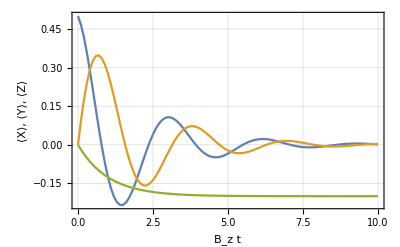

```mathematica
data=Transpose@Table[
{{t,avgX[t]},{t,avgY[t]},{t,avgZ[t]}},
{t,0,10,0.1}
];
ListLinePlot[data,
FrameLabel->{"B_z t","⟨X⟩, ⟨Y⟩, ⟨Z⟩"}
]
```

Consider a three-level atom with the Λ-type level structure.

```mathematica
Let[Qudit,A]
```

In the interaction picture, the Hamiltonian looks like this. We have put the two Rabi transition amplitudes to 1.

```mathematica
opH=(1/10)A[1->1]+(2/10)A[2->2]+A[2->0]+A[0->2]+A[2->1]+A[1->2];
matH=Matrix[opH];
matH//MatrixForm
```

(0 | 0 | 1
0 | 1/10 | 1
1 | 1 | 1/5)

```mathematica
Let[Real,Γ]
opL={
Sqrt[Γ[0,"-"]]*A[2->0],
Sqrt[Γ[0,"+"]]*A[0->2],
Sqrt[Γ[1,"-"]]*A[2->1],
Sqrt[Γ[1,"+"]]*A[1->2]}
matL=Matrix[opL];
MatrixForm/@matL
```

{(02) √(Γ_(0,-)),(20) √(Γ_(0,+)),(12) √(Γ_(1,-)),(21) √(Γ_(1,+))}

{(0 | 0 | √(Γ_(0,-))
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
√(Γ_(0,+)) | 0 | 0),(0 | 0 | 0
0 | 0 | √(Γ_(1,-))
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | √(Γ_(1,+)) | 0)}

```mathematica
Timing[
ρ[t_]=Block[
{Γ,init},
Γ[0,"-"]=0.05;
Γ[0,"+"]=0.01;
Γ[1,"-"]=0.025;
Γ[1,"+"]=0.005;
init=DiagonalMatrix[{0,1,0}];
LindbladSolve[matH,matL,init,t]
];
]
```

{2.99647,Null}

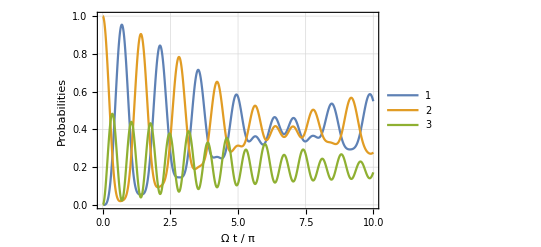

```mathematica
Plot[Evaluate@Diagonal@ρ[t Pi],{t,0,10},
FrameLabel->{"Ω t / π","Probabilities"},
PlotRange->All,
PlotLegends->Automatic]
```

## Fidelity and Trace Distance

## Entanglement, Entropy, Mutual Information